# Potential and Fields

Electric field and potential inside a hollow metallic prism with a solid, metallic inner conductor.

561

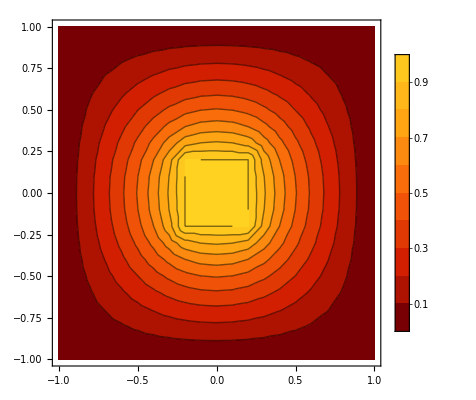

-Graphics3D-

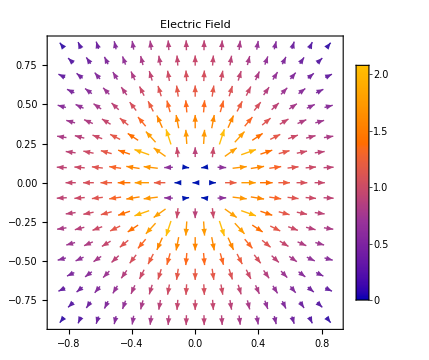

```mathematica
ClearAll["Global`*"];
xMax=1.0;xMin=-1.0; yMax=1.0;yMin=-1.0;vMax=1.0;vMin=0; npt=20;vnpt=8;
dy=dx=(xMax-xMin)/npt;
yl=xl=Range[xMin,xMax,dx];ly=lx=Length[xl];
vMat=ConstantArray[0,{lx,ly}];

Do[vMat[[i,j]]=1,{j,vnpt,lx-vnpt},{i,vnpt,ly-vnpt}]; (*Creating the inner conductor*)
v00=vMat//MatrixForm;

e=10^-20;
diff=01;
n=0;

While[diff≥e,

Do[
vMat[[i,j]]=(vMat[[i+1,j]]+vMat[[i-1,j]]+vMat[[i,j+1]]+vMat[[i,j-1]])/4;
,{i,2,lx-1},{j,2,vnpt}];
Do[
vMat[[i,j]]=(vMat[[i+1,j]]+vMat[[i-1,j]]+vMat[[i,j+1]]+vMat[[i,j-1]])/4;
,{i,2,vnpt},{j,vnpt,lx-1}];
Do[
vMat[[i,j]]=(vMat[[i+1,j]]+vMat[[i-1,j]]+vMat[[i,j+1]]+vMat[[i,j-1]])/4;
,{i,2,lx-1},{j,vnpt+6,ly-1}];
Do[
vMat[[i,j]]=(vMat[[i+1,j]]+vMat[[i-1,j]]+vMat[[i,j+1]]+vMat[[i,j-1]])/4;
,{i,vnpt+6,lx-1},{j,2,ly-1}];


diff=Max[Abs[vMat-v0]];v0=vMat;
n=n+1];

vMat//MatrixForm;
n
p1 =ListContourPlot[Reverse[vMat],DataRange->{{-1,1},{-1,1}},ColorFunction->"SolarColors",PlotLegends->Automatic]
ListPlot3D[vMat,DataRange->{{0,lx},{0,ly}},AspectRatio->1,Mesh->All,PlotLabel->"V",PlotTheme->"Business"]

ef=ConstantArray[0,{lx,ly}];
Do[ef[[i,j]]=-1/(2dx){(vMat[[i+1,j]]-vMat[[i-1,j]]),(vMat[[i,j+1]]-vMat[[i,j-1]])},{i,2,lx-1},{j,2,ly-1}]
ListVectorPlot[Table[{{xl[[i]],xl[[j]]},ef[[i,j]]},{i,2,lx-1},{j,2,lx-1}],PlotLegends->Automatic, VectorScaling->Large,PlotLabel->"Electric Field",ImageSize->Medium]
```

Electric field and potential near a point charge located at the center of a grounded metal box.

```mathematica
ClearAll["Global`*"];
smax=1;ds=0.1;
m=2 smax/ds;(*The step numbers*)
sl=Range[-smax,smax,ds]; ls=Length[sl];
vmat=rho=ConstantArray[0,{ls,ls,ls}];
n=0;v0=vmat;
rho[[m/2+1,m/2+1,m/2+1]]=ds^3;

e=10^-10;diff=01;

While[diff≥e,

Do[
vmat[[i,j,k]]=(vmat[[i-1,j,k]]+vmat[[i+1,j,k]]+vmat[[i,j-1,k]]+vmat[[i,j+1,k]]+vmat[[i,j,k-1]]+vmat[[i,j,k+1]])/6+(rho[[i,j,k]] ds^2)/6,{i,2,ls-1},{j,2,ls-1},{k,2,ls-1}];

diff=Max[Abs[vmat-v0]];v0=vmat;
n=n+1];
vmat//MatrixForm;
n
(*Plottting Voltage*)
t= Flatten[Table[{sl[[i]],sl[[j]],vmat[[i,j,m/2]]},{i,ls},{j,ls}],1];

p1 =ListContourPlot[t,ColorFunction->"SolarColors",PlotLegends->Automatic,AxesLabel->{"x","y"},ImageSize->Medium];
p2= ListContourPlot[vmat,DataRange->{{-0.4,0.4},{-0.4,0.4}},PlotLegends->Automatic,ColorFunction-> "DarkRainbow",PlotLabel->"Equipotential lines around a point charge in 3D",ImageSize->Medium];
GraphicsRow[{p1,p2},ImageSize->Full]
p3=ListPlot3D[t,AspectRatio->1,PlotRange->All,Mesh->All,AxesLabel->{"x","y"},PlotLabel->"V",PlotTheme->"Business"];
(*Plottting Electric Field in the x-y plane*)
ef =ConstantArray[0,{ls,ls}];
Do[
ef[[i,j]]=-1/(2ds){(vmat[[i+1,j,m/2]]-vmat[[i-1,j,m/2]]),(vmat[[i,j+1,m/2]]-vmat[[i,j-1,m/2]])},{i,2,ls-1},{j,2,ls-1}];
p4=ListVectorPlot[Table[{{sl[[i]],sl[[j]]},ef[[i,j]]},{i,2,ls-1},{j,2,ls-1}],Axes->True,AxesLabel->{"x","y"},PlotLegends->Automatic, VectorScaling->Large,PlotLabel->"Field lines around a point charge in 3D",ImageSize->Medium];
GraphicsRow[{p3,p4},ImageSize->Full]
```

143

-Graphics-

-Graphics-

Magnetic field produced by a current loop, on the axis of the loop.

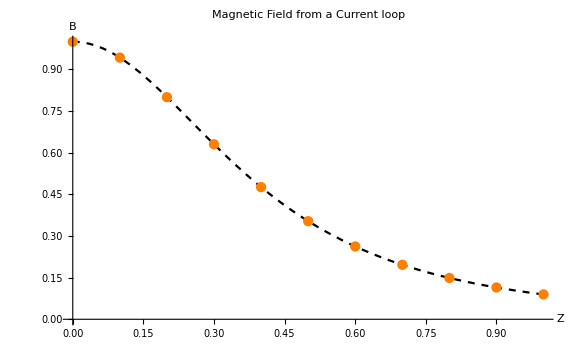

```mathematica
ClearAll["Global`*"];
zmin=0;zmax=1; dz=0.1;
r=0.5;dth=2π/10;
th=Range[0,2π,dth];lth=Length[th];
Magn=0*th;
zl=Range[zmin,zmax,dz];lz=Length[zl];
B[z_]=r^2/(2(r^2+z^2)^(3/2)); (*Exact*)
Do[Magn[[i]]= r^2/(4.0 π (zl[[i]]^2+r^2)^(3/2))(∑_(j=1)^10 dth),{i,lz}]
p1=Plot[B[z],{z,zmin,zmax},LabelStyle->{FontSize->13,FontFamily->"Times",RGBColor[0,0,0]},RotateLabel->False,PlotStyle->{Black,Dashed},GridLines->None,ImageSize->Large,PlotLabel->"Magnetic Field from a Current loop"];

p2=ListPlot[Table[{zl[[k]],Magn[[k]]},{k,lz}], PlotStyle->Orange];
Show[p1,p2, AxesLabel->{"Z","B"}]
```

Numerical solution(Trial) for the Magnetic Field in the z-direction

20

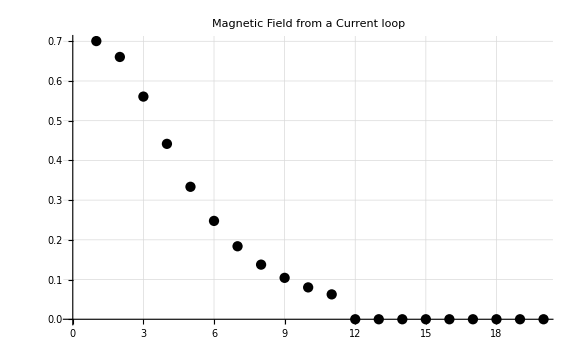

```mathematica
ClearAll["Global`*"];
ds=0.1;r=0.5;
x=Range[r,-r,-ds];lx=Length[x];
(*Making x list*)
xl=Flatten[AppendTo[x,-x[[2;;lx-1]]]];lxl=Length[xl]
zl=Range[0r,2r,ds];lz=Length[zl];
Magnz=Magn=dtot=rl=dll=yl=0xl;
(*Making y list*)
Do[And[If[n≤lxl/2,yl[[n]]=√(r^2-(xl[[n]])^2)],If[n>lxl/2,yl[[n]]=-√(r^2-(xl[[n]])^2)]],{n,lxl}]; 


(*Making unit vectors list in the dl direction *)
Do[
k={0,0,1};m={xl[[n]],yl[[n]],0};
dll[[n]]=1/r Cross[k,m],{n,lxl}];


Do[

Do[
(*Making  vectors list in the R direction *)
rl[[n]]={-xl[[n]],-yl[[n]],zl[[i]]};
(*getting the dl magnitude for each point in the loop*)
dtot[[n]]=√(ds^2(1+xl[[n]]^2/(r^2+xl[[n]]^2)));
Magn[[n]]=1/(4π)(dtot[[n]]/((r^2+zl[[i]]^2)^(3/2)))Cross[dll[[n]],rl[[n]]];

,{n,lxl}];

Magnz[[i]]=Sum[Magn[[a,3]],{a,lxl}]
,{i,lz}]

ListPlot[{Magnz},GridLines->Automatic,PlotStyle-> Black,PlotLabel->"Magnetic Field from a Current loop",LabelStyle->{FontSize->10,FontFamily->"Helvetica",RGBColor[0,0,0]},ImageSize->Large]
```